```mathematica
template = { {+1,-1,0},{+1,-1,0},{0,0,0},{0,-1,+1},{0,-1,+1}}
Ns = Length[template]
w=template[[1]]//Length
```

{{1,-1,0},{1,-1,0},{0,0,0},{0,-1,1},{0,-1,1}}

5

3

```mathematica
σ2Em1 = Table[ Table[ Table[ Table[ KroneckerDelta[l,m]KroneckerDelta[a,b] -1/(Ns+1)  KroneckerDelta[l,m],{b,1,Ns}],{m,1,w}] ,{a,1,Ns}],{l,1,w}];
```

```mathematica
fσ2Em1[{a_,l_},{b_,m_}] :=  KroneckerDelta[l,m]KroneckerDelta[a,b] -1/(Ns+1)  KroneckerDelta[l,m]
```

```mathematica
processedTemplate[{a_,l_}]:= Sum[ fσ2Em1[{a,l},{b,m}] template[[b,m]],{b,1,Ns},{m,1,w}]
```

```mathematica
procTempResult=Table[ processedTemplate[{a,l}], {a,1,Ns},{l,1,w}]//N
```

{{0.666667,-0.333333,-0.333333},{0.666667,-0.333333,-0.333333},{-0.333333,0.666667,-0.333333},{-0.333333,-0.333333,0.666667},{-0.333333,-0.333333,0.666667}}

```mathematica
MatrixPlot[procTempResult,Mesh->All]
```

-Graphics-

```mathematica
template
```

{{1,-1,0},{1,-1,0},{0,0,0},{0,-1,1},{0,-1,1}}

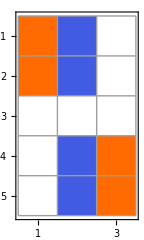

```mathematica
MatrixPlot[{{1,-1,0},{1,-1,0},{0,0,0},{0,-1,1},{0,-1,1}},Mesh->All]
```